```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v2

```mathematica
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,0,870,10}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,0,870,10}];
r42=chi4/chi2;
```

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

```mathematica
r42[[1;;45]][[1;;60]]=1;
r42[[46;;55]][[1;;50]]=1;
r42[[56;;62]][[1;;40]]=1;
r42[[63;;78]][[1;;20]]=1;
r42[[79;;84]][[1;;15]]=1;
r42[[85;;88]][[1;;10]]=1;
```

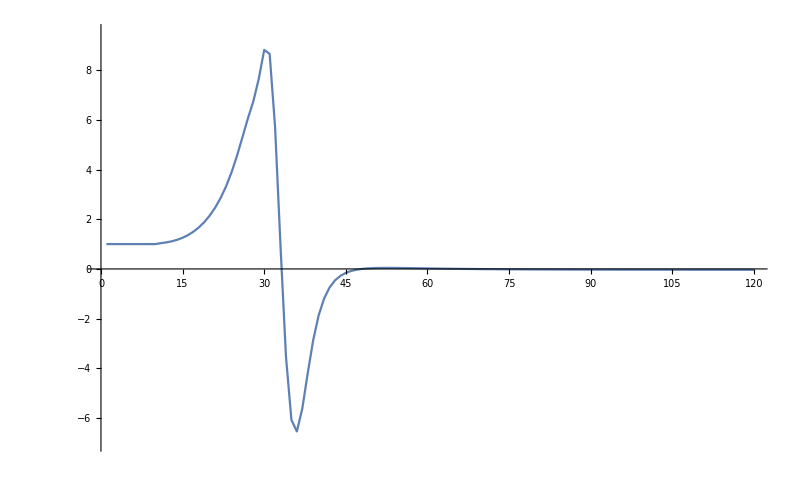

```mathematica
ListLinePlot[r42[[-1]],PlotRange->{All,{-7,9.5}}]
```

```mathematica
ListDensityPlot[Transpose[r42],PlotRange->{All,All,{-5,5}}]
```

-Graphics-